```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"]
data1={0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0};
data2={1,0,1,1,0,1,1,1,0,0,0,1,1,1,1,1,0,0,0,0,0,1,1,0,1,1,1,1,1,1,1,0,0,0,1,1,1,1,1,0,0,0,0,1,1,1,1,0,1,1,1,0,1,1,1,0,0,0,0,0,1,0,1,1,0,1,1,1,0,1,0,0,1,0,0,1,1,0,0,0,0,0,1,0,1,1,1,1,0,1,1,0,1,1,1,0,0,1,0,1};
```

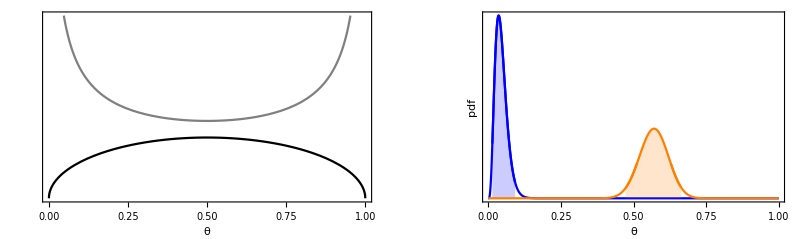

```mathematica
n = 100;(*
data1=RandomVariate[BernoulliDistribution[0.1],{n}];
data2=RandomVariate[BernoulliDistribution[0.5],{n}];*)
aPost1 = BetaDistribution[0.5+Total@data1,0.5+n-Total@data1];
aPost2 = BetaDistribution[0.5+Total@data2,0.5+n-Total@data2];
g2=Module[{aLower1=Quantile[aPost1,0.025],aUpper1=Quantile[aPost1,0.975],aLower2=Quantile[aPost2,0.025],aUpper2=Quantile[aPost2,0.975]},Show[Plot[{PDF[aPost1,x]},{x,0,1},PlotRange->Full,PlotStyle->Blue,Frame->{True,True,False,False},FrameTicks->{True,None},FrameLabel->{"θ","pdf"},BaseStyle->{FontSize->16}],Plot[{PDF[aPost1,x]},{x,aLower1,aUpper1},PlotStyle->Blue,Filling->Axis,Frame->{True,True,False,False},FrameTicks->{True,None},FrameLabel->{"θ",},BaseStyle->{FontSize->16}],Plot[{PDF[aPost2,x]},{x,0,1},PlotStyle->Orange,Frame->{True,True,False,False},FrameTicks->{True,None},FrameLabel->{"θ",},BaseStyle->{FontSize->16}],Plot[{PDF[aPost2,x]},{x,aLower2,aUpper2},PlotStyle->Orange,Filling->Axis,PlotRange->{Automatic,{0,10}},Frame->{True,True,False,False},FrameTicks->{True,None},FrameLabel->{"θ",},BaseStyle->{FontSize->16}]]];
fFindCentralPosteriorInt[aDist_]:=Module[{aUpper,aLower},aLower = Quantile[aDist,0.025];aUpper = Quantile[aDist,0.975];aUpper-aLower]
g1=Plot[{StandardDeviation@BernoulliDistribution[θ],PDF[BetaDistribution[0.5,0.5],θ]},{θ,0,1},PlotStyle->{Black,Gray},Frame->{True,True,False,False},FrameTicks->{True,None},FrameLabel->{"θ",},BaseStyle->{FontSize->16}];
gFinal=Show[GraphicsRow[{g1,g2}],ImageSize->800]
```

```mathematica
Export["Objective_jeffreysBeta.pdf",gFinal]
```

Objective_jeffreysBeta.pdf